```mathematica
limitation = 32;
limit=(limitation+2);
limitHalf=(limitation/2);

epimoricRatios = {(# + 1)/#} & [ Range[1,limitation]] // Flatten ;
reciprocalRatios = {#/(# +1)} & [Range[1,limitation]] // Flatten ;

invertedEpimorics = inverter /@ epimoricRatios  ;
invertedReciprocals = inverterReciprocal /@ reciprocalRatios ;

tones = Association[0->{"UNISON","FIXED"},1->{"MINOR 2ND","MOVABLE"}, 2->{"MAJOR 2ND","MOVABLE"}, 3->{"MINOR 3RD","MOVABLE"}, 4->{"MAJOR 3RD","MOVABLE"}, 5->{"PERFECT 4TH","FIXED"}, 6->{"TRITONE","MOVABLE"}, 7->{"PERFECT 5TH","FIXED"}, 8->{"MINOR 6TH","MOVABLE"}, 9->{"MAJOR 6TH","MOVABLE"}, 10->{"MINOR 7TH","MOVABLE"}, 11->{"MAJOR 7TH","MOVABLE"}, 12->{"DIAPESON","FIXED"}];


foundEpimorics= List[] ;
epimoricKinship = List[] ;
reciprocalKinship = List[];
epimoricRelations = List[] ;
reciprocalRelations = List[]  ;
epimoricProgeny = List[];
reciprocalProgeny = List[] ;


For[x=1,x<limitHalf,x++,With[{y=(x*2),z=(x*2)+1},AppendTo[epimoricKinship,{epimoricRatios[[x]]<->epimoricRatios[[y]],epimoricRatios[[x]]<->epimoricRatios[[z]]}]]];

For[x=1,x<limitHalf,x++, With[{y=(x*2),z=(x*2)+1},AppendTo[reciprocalKinship,{reciprocalRatios[[x]]<->reciprocalRatios[[y]],reciprocalRatios[[x]]<->reciprocalRatios[[z]]}]]] ;

For[i=1,i<limitation,i++,For[n=1,n<limitation,n++,AppendTo[epimoricProgeny,{epimoricRatios[[i]]<->epimoricRatios[[i]]*epimoricRatios[[n]],epimoricRatios[[n]]<->epimoricRatios[[n]]*epimoricRatios[[i]]}]]];

For[i=1,i<limitation,i++,For[n=1,n<limitation,n++,AppendTo[reciprocalProgeny,{reciprocalRatios[[i]]<->reciprocalRatios[[i]]*reciprocalRatios[[n]],reciprocalRatios[[n]]<->reciprocalRatios[[n]]*reciprocalRatios[[i]]}]]];


epimoricRelations=VertexList[Flatten[epimoricProgeny]] ;
reciprocalRelations = VertexList[Flatten[reciprocalProgeny]] ;
combinedProgeny = Union[epimoricRelations,reciprocalRelations] ;
combined = Union[epimoricRatios, combinedProgeny];
combined2 = Union[combined, reciprocalRatios ] ;
combined3 = Union[combined2, invertedEpimorics ] ;
combined4 = Union[combined3, invertedReciprocals] ;
octavized = combined4 /. num_ /; num > 2/1 -> num / 2  ;
octavized2 = octavized /. z_ /; z  <  1/1 -> z * 2;
octavized3 = octavized2 //.  { _>2->_/2, _<1->_*2} ;
(*sorted = SortBy[octavized3, N] ;*)
allRatios = octavized3 /. z_ /; z < 1 -> z * 2 ;
collected = SortBy[allRatios,N] // DeleteDuplicates ;
(*Select[collected, 5/3 < # < 2/1 & ]  *)

Unprotect[knownRatios];

Protect[knownRatios] ;
referencedRatios=Keys[knownRatios] ;
tested = Intersection[referencedRatios, collected]  ;
Length[tested];
Length[knownRatios];

pairNeighbors[notes_] :=Partition[notes,2,1] ;
discoverIntervals[{x_,y_}]:= y/x ;
noteRatios[x_] :=Rest[FoldList[Times,1,x]] ;
discoverEpimorics[candidate_]:= If[(Numerator[candidate]-Denominator[candidate])==1,AppendTo[foundEpimorics,candidate],Continue];
inverter[ratio_] := 2/ratio ;
inverterReciprocal[ratio_] := 1/2 / ratio ;


identify[ratio_]:=If[MemberQ[referencedRatios,ratio],Echo[knownRatios[ratio],ToString[StandardForm[ratio]]<>": "],Echo[ToString[StandardForm[ratio]],Continue]] ;


divider[ratio_] := With[{a = Numerator[ratio] * 2 , b = Denominator[ratio] * 2 , c =  Denominator[ratio] * 2 + 1 } ,  {c/b , a/c}] ;

inverter[14/13]
inverter[7/6]
inverter[19/15]
inverter[9/7]
(*knownRatios[250/243]
divider[9/8]
inverter[27/25]
inverter[10/9]*)
```

13/7

12/7

30/19

14/9

{14/13,13/12,38/35,135/133,28/27,18/17,17/16,28/27,135/133,38/35,13/12,14/13}

-Graphics-

-Graphics-

-Graphics-

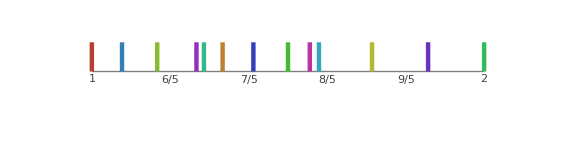

```mathematica
(*example = Association[0->1/1,1->16/15,2->10/9,3->6/5,4->5/4,5->4/3,6->24/17,7->3/2,8->8/5,9->5/3,10->9/5,11->15/8,12->2/1] ;*)
example = Association[0->1/1,1->14/13,2->7/6,3->19/15,4->9/7,5->4/3,6->24/17,7->3/2,8->14/9,9->30/19,10->12/7,11->13/7,12->2/1] ;

pairs = pairNeighbors[Values[example]] ;
intraNoteRatios = discoverIntervals /@ pairs  
intervalRatios = Interval /@ pairs;
 
noteList = noteRatios[intraNoteRatios]  ;
 

notes = AssociationThread[Range[1,12],noteList];
PrependTo[notes,0->1/1] ;
PrependTo[noteList, 1/1] ;

GraphicsColumn[{GraphTree[TreeGraph[Flatten[epimoricKinship ]],TreeLayout->Bottom, ImageSize->1000],GraphTree[TreeGraph[Flatten[reciprocalKinship ]],TreeLayout-> Top,ImageSize -> 1000]},ImageSize -> Large]

discoverEpimorics /@ noteList ;

(*identify /@ noteList ;
identify /@ invertedEpimorics ;*)

HighlightGraph[TreeGraph[Flatten[epimoricKinship],
GraphLayout->"LayeredDrawing",PlotTheme->"Scientific",ImageSize->Large,
VertexShapeFunction->{"Circle"},VertexSize->{{"Scaled",0.04}},VertexLabels->Placed["Name",{1/2,1/2}]],Style[foundEpimorics,Green]]

HighlightGraph[TreeGraph[Flatten[epimoricKinship],
GraphLayout->"LayeredDrawing",PlotTheme->"Scientific",ImageSize->Large,
VertexShapeFunction->{"Circle"},VertexSize->{{"Scaled",0.04}},VertexLabels->Placed["Name",{1/2,1/2}]],Style[intraNoteRatios,Red]]

HorizontalGauge[Flatten[noteList],{1,2},GaugeMarkers -> "BarMarker", ScaleDivisions -> 5, ImageSize->Large]
(*HorizontalGauge[Flatten[noteList],{1,2}, ScaleRanges->{{1,16/15} -> Red, {16/15,10/9} ->Orange ,{10/9, 6/5} ->Yellow, {6/5,5/4}->Orange, {5/4, 4/3} -> Red},GaugeMarkers -> "BarMarker", ScaleDivisions -> 5, ImageSize->1500]*)

Manipulate[Dynamic[{MINOR2ND,MAJOR2ND,MINOR3RD,MAJOR3RD,TRITONE,MINOR6TH,MAJOR6TH,MINOR7TH,MAJOR7TH}],  Delimiter, Style["UNISON - 1/1",14,Bold],Delimiter,{MINOR2ND,Select[collected,1<#< 4/3 & ], ControlType->TogglerBar}, {MAJOR2ND,  Select[collected, 1 < # <  4/3&], ControlType->TogglerBar}, {MINOR3RD, Select[collected, 1< # < 4/3 &], ControlType->TogglerBar },{MAJOR3RD, Select[collected,1 < # < 4/3 &],ControlType->TogglerBar},
Delimiter, Style["PERFECT 4TH - 4/3",14,Bold],Delimiter,{TRITONE, Select[collected,4/3< # < 3/2 &] ,ControlType->TogglerBar },Delimiter, Style["PERFECT 5TH - 3/2",14,Bold],Delimiter,{MINOR6TH, Select[collected,3/2 < # < 2 &], ControlType->TogglerBar },{MAJOR6TH, Select[collected, 3/2< # < 2 &],ControlType->TogglerBar},{MINOR7TH, Select[collected, 3/2 < # < 2&],ControlType->TogglerBar },{MAJOR7TH, Select[collected, 3/2< # < 2 & ], ControlType->TogglerBar}, Delimiter, Style["DIAPESON - 2/1",14,Bold], Delimiter]
```